# C++ Class Layout Parser - Comprehensive Inheritance Testing

This notebook demonstrates the C++ Class Layout Parser tool by testing various inheritance patterns and visualizing memory layouts. The parser uses clang's JSON AST via CppClassLayoutParser.wl.

## Setup and Initialization

```mathematica
(* Clear definitions and load parser *)
Remove["CppClassLayoutParser`*"];
SetDirectory[NotebookDirectory[]];
<< "../CppClassLayoutParser.wl"
```

## Test Overview Table

```mathematica
{{"Test #", "Pattern", "Description", "File", "Target Class"}, {"Test 1", "Simple Single Class", "Basic VTable creation", "simple_single_class.hpp", "SimpleClass"}, {"Test 2", "Single Inheritance", "Basic inheritance hierarchy", "single_inheritance.hpp", "Derived"}, {"Test 3", "Multiple Inheritance", "Multiple base classes", "multiple_inheritance.hpp", "MultipleDerived"}, {"Test 4", "Virtual Inheritance", "Shared virtual bases", "virtual_inheritance.hpp", "VirtualMultiple"}, {"Test 5", "Diamond Inheritance", "Classic diamond problem", "diamond_inheritance.hpp", "DiamondBottom"}, {"Test 6", "Complex Inheritance", "Mixed virtual/non-virtual", "complex_inheritance.hpp", "Z"}, {"Test 7", "Deep Inheritance", "5-level hierarchy", "deep_inheritance.hpp", "Level5"}, {"Test 8", "Interface Inheritance", "Abstract classes", "interface_inheritance.hpp", "MultiInterface"}, {"Test 9", "Template Inheritance", "Template instantiation", "template_inheritance.hpp", "DoubleDerived"}, {"Test 10", "Extreme Complexity", "Multiple virtual bases & deep hier.", "extreme_complexity.hpp", "UltimateComplex"}}
```

## Test 1: Simple Single Class

=== Contents of “simple_single_class.hpp” ===

// Simple single class with virtual functions
class SimpleClass {
public:
    virtual void method1() {}
    virtual void method2() {}
    virtual ~SimpleClass() {}
    
private:
    int data1;
    double data2;
};

=== Layout for “SimpleClass” ===

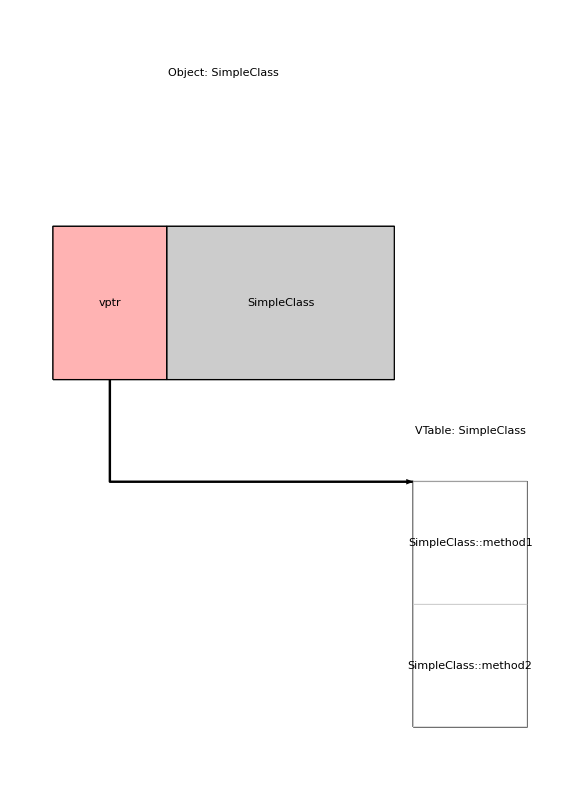

```mathematica
(* Basic VTable creation *)
(* 1. Read and print the C++ source file *)
code = Import["simple_single_class.hpp", "Text"];
Print["=== Contents of “simple_single_class.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["simple_single_class.hpp", "SimpleClass"];
Print["=== Layout for “SimpleClass” ==="];
Print[result];
```

## Test 2: Single Inheritance

=== Contents of “single_inheritance.hpp” ===

// Single inheritance example
class Base {
public:
    virtual void baseMethod() {}
    virtual ~Base() {}
    
private:
    int baseData;
};

class Derived : public Base {
public:
    virtual void derivedMethod() {}
    virtual void baseMethod() override {}
    virtual ~Derived() {}
    
private:
    double derivedData;
};

=== Layout for “Derived” ===

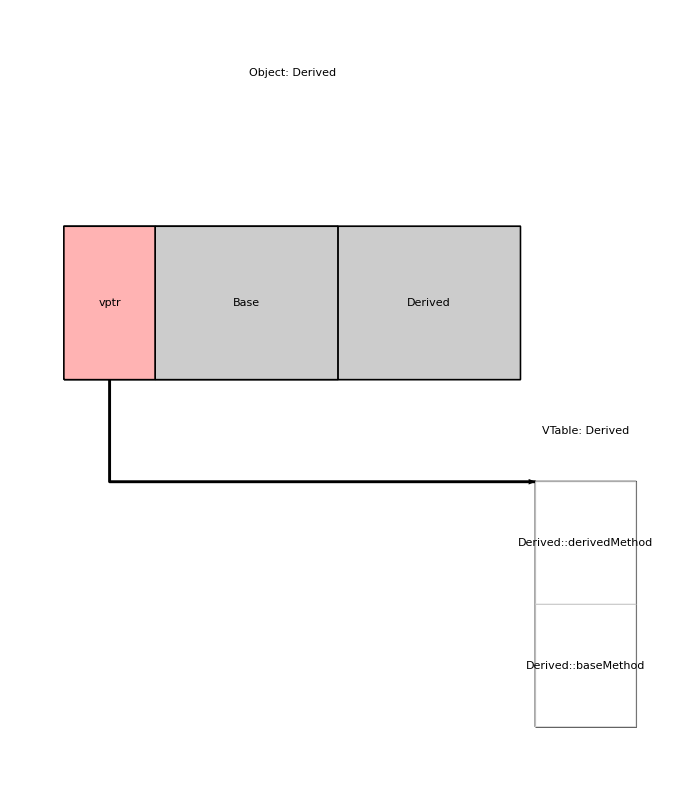

```mathematica
(* Basic inheritance hierarchy *)
(* 1. Read and print the C++ source file *)
code = Import["single_inheritance.hpp", "Text"];
Print["=== Contents of “single_inheritance.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["single_inheritance.hpp", "Derived"];
Print["=== Layout for “Derived” ==="];
Print[result];
```

## Test 3: Multiple Inheritance

=== Contents of “multiple_inheritance.hpp” ===

// Multiple inheritance example
class Base1 {
public:
    virtual void base1Method() {}
    virtual ~Base1() {}
    
private:
    int base1Data;
};

class Base2 {
public:
    virtual void base2Method() {}
    virtual ~Base2() {}
    
private:
    double base2Data;
};

class MultipleDerived : public Base1, public Base2 {
public:
    virtual void derivedMethod() {}
    virtual void base1Method() override {}
    virtual void base2Method() override {}
    virtual ~MultipleDerived() {}
    
private:
    char derivedData;
};

=== Layout for “MultipleDerived” ===

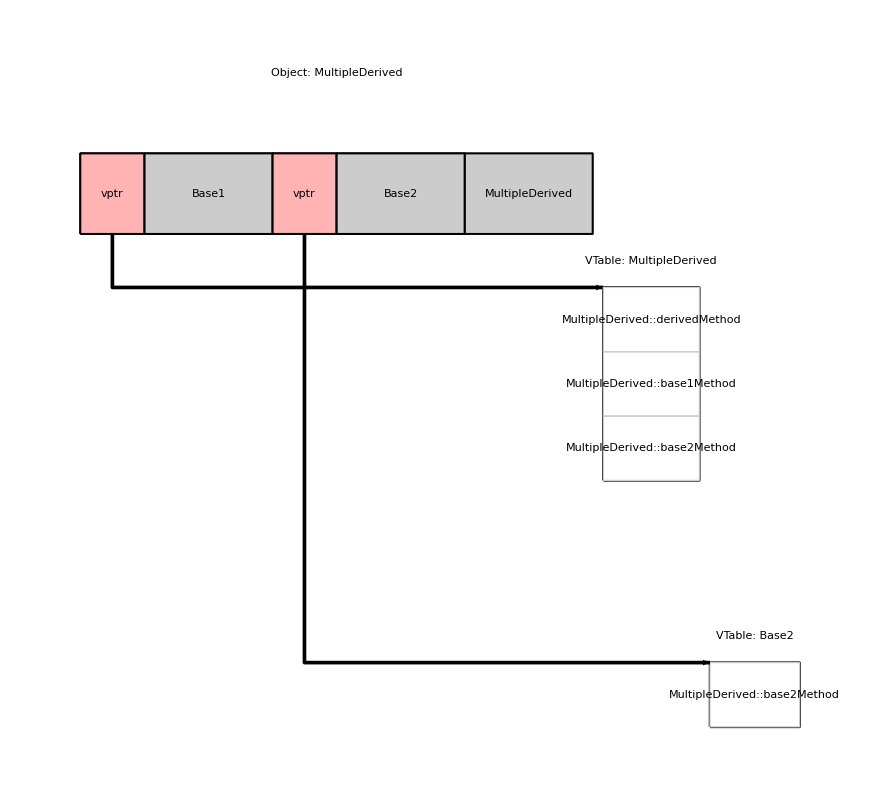

```mathematica
(* Multiple base classes *)
(* 1. Read and print the C++ source file *)
code = Import["multiple_inheritance.hpp", "Text"];
Print["=== Contents of “multiple_inheritance.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["multiple_inheritance.hpp", "MultipleDerived"];
Print["=== Layout for “MultipleDerived” ==="];
Print[result];
```

## Test 4: Virtual Inheritance

=== Contents of “virtual_inheritance.hpp” ===

// Virtual inheritance example
class VirtualBase {
public:
    virtual void virtualBaseMethod() {}
    virtual ~VirtualBase() {}
    
private:
    int virtualBaseData;
};

class VirtualDerived1 : virtual public VirtualBase {
public:
    virtual void derived1Method() {}
    virtual ~VirtualDerived1() {}
    
private:
    double derived1Data;
};

class VirtualDerived2 : virtual public VirtualBase {
public:
    virtual void derived2Method() {}
    virtual ~VirtualDerived2() {}
    
private:
    char derived2Data;
};

class VirtualMultiple : public VirtualDerived1, public VirtualDerived2 {
public:
    virtual void multipleMethod() {}
    virtual ~VirtualMultiple() {}
    
private:
    float multipleData;
};

=== Layout for “VirtualMultiple” ===

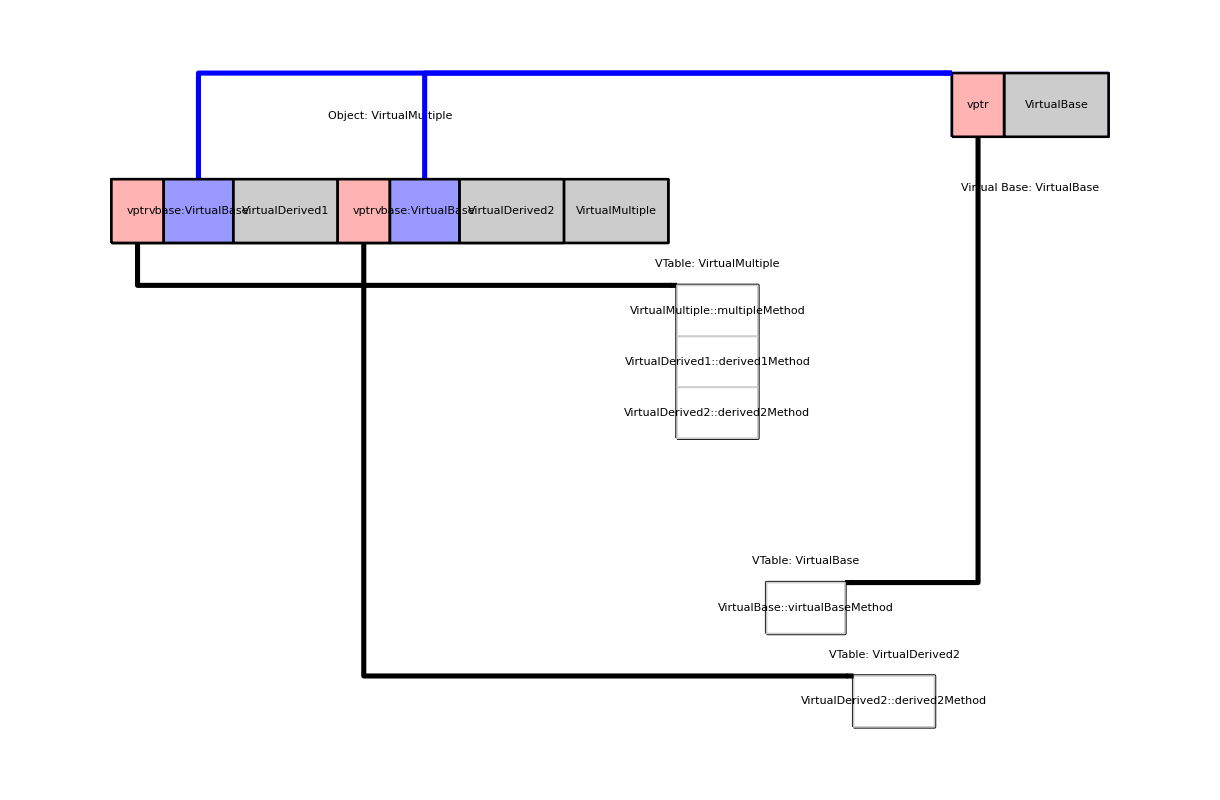

```mathematica
(* Shared virtual bases *)
(* 1. Read and print the C++ source file *)
code = Import["virtual_inheritance.hpp", "Text"];
Print["=== Contents of “virtual_inheritance.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["virtual_inheritance.hpp", "VirtualMultiple"];
Print["=== Layout for “VirtualMultiple” ==="];
Print[result];
```

## Test 5: Diamond Inheritance

=== Contents of “diamond_inheritance.hpp” ===

// Classic diamond inheritance problem
class DiamondBase {
public:
    virtual void diamondMethod() {}
    virtual ~DiamondBase() {}
    
private:
    int diamondData;
};

class DiamondLeft : virtual public DiamondBase {
public:
    virtual void leftMethod() {}
    virtual void diamondMethod() override {}
    virtual ~DiamondLeft() {}
    
private:
    double leftData;
};

class DiamondRight : virtual public DiamondBase {
public:
    virtual void rightMethod() {}
    virtual void diamondMethod() override {}
    virtual ~DiamondRight() {}
    
private:
    char rightData;
};

class DiamondBottom : public DiamondLeft, public DiamondRight {
public:
    virtual void bottomMethod() {}
    virtual void diamondMethod() override {}
    virtual ~DiamondBottom() {}
    
private:
    float bottomData;
};

=== Layout for “DiamondBottom” ===

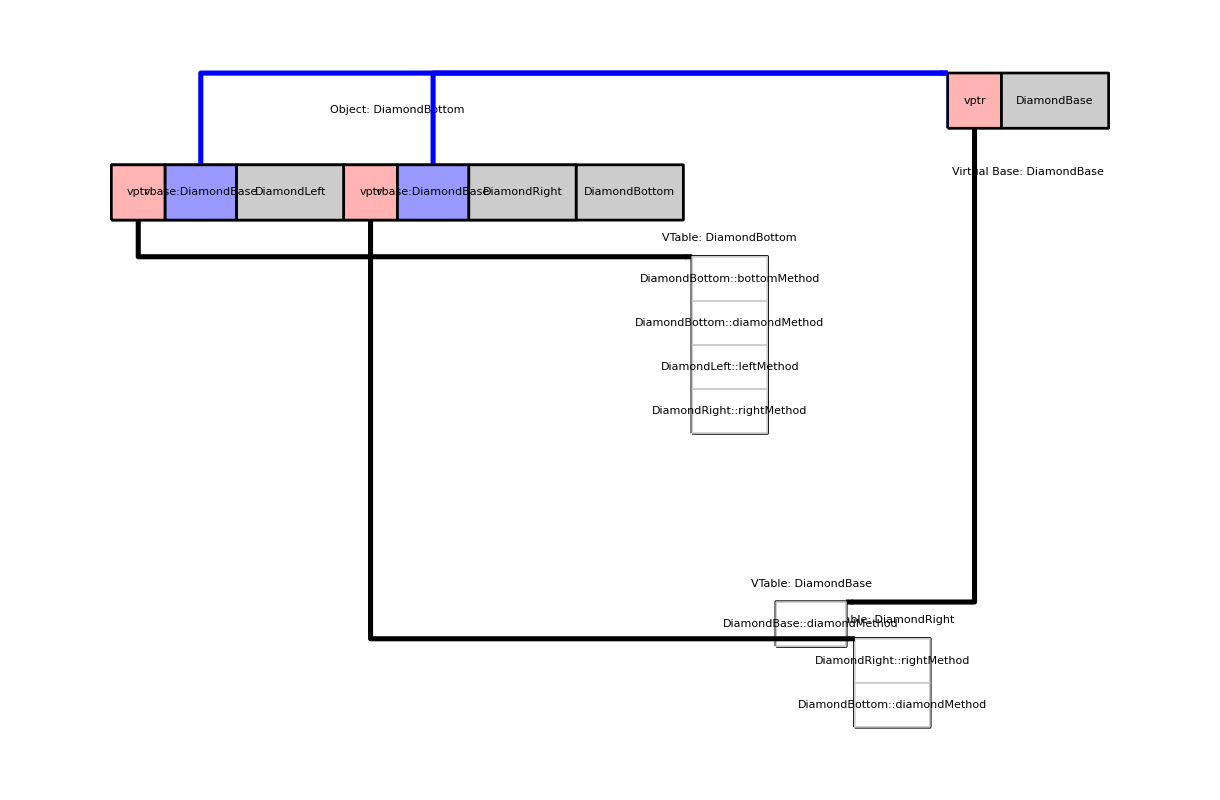

```mathematica
(* Classic diamond problem *)
(* 1. Read and print the C++ source file *)
code = Import["diamond_inheritance.hpp", "Text"];
Print["=== Contents of “diamond_inheritance.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["diamond_inheritance.hpp", "DiamondBottom"];
Print["=== Layout for “DiamondBottom” ==="];
Print[result];
```

## Test 6: Complex Inheritance

=== Contents of “complex_inheritance.hpp” ===

// Complex inheritance with mixed virtual and non-virtual inheritance
class X {
public:
    virtual void xMethod() {}
    virtual ~X() {}
    
private:
    int xData;
};

class Y1 : public X {
public:
    virtual void y1Method() {}
    virtual void xMethod() override {}
    virtual ~Y1() {}
    
private:
    double y1Data;
};

class Y2 : virtual public X {
public:
    virtual void y2Method() {}
    virtual void xMethod() override {}
    virtual ~Y2() {}
    
private:
    char y2Data;
};

class Z : public Y1, public Y2 {
public:
    virtual void zMethod() {}
    virtual void xMethod() override {}
    virtual ~Z() {}
    
private:
    float zData;
};

=== Layout for “Z” ===

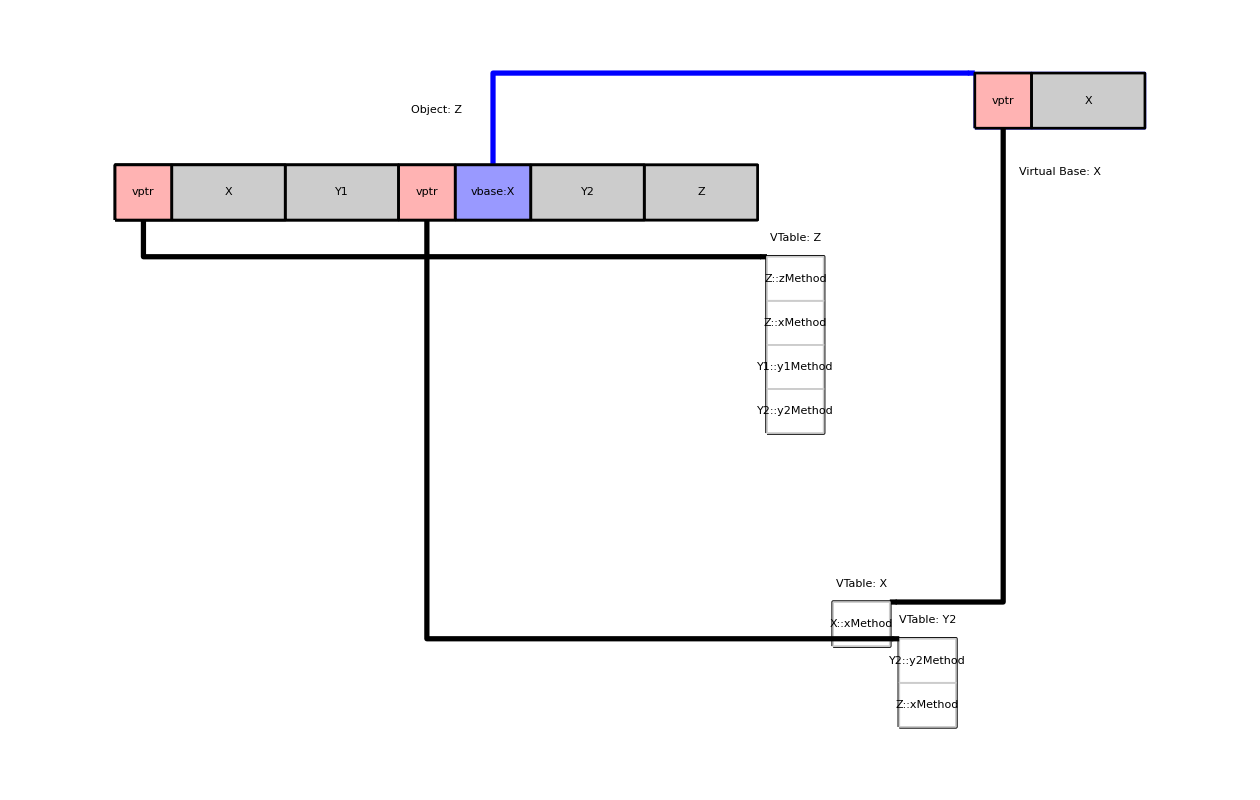

```mathematica
(* Mixed virtual/non-virtual *)
(* 1. Read and print the C++ source file *)
code = Import["complex_inheritance.hpp", "Text"];
Print["=== Contents of “complex_inheritance.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["complex_inheritance.hpp", "Z"];
Print["=== Layout for “Z” ==="];
Print[result];
```

## Test 7: Deep Inheritance

```mathematica
(* 5-level hierarchy *)
(* 1. Read and print the C++ source file *)
code = Import["deep_inheritance.hpp", "Text"];
Print["=== Contents of “deep_inheritance.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["deep_inheritance.hpp", "Level5"];
Print["=== Layout for “Level5” ==="];
Print[result];
```

## Test 8: Interface Inheritance

```mathematica
(* Abstract classes *)
(* 1. Read and print the C++ source file *)
code = Import["interface_inheritance.hpp", "Text"];
Print["=== Contents of “interface_inheritance.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["interface_inheritance.hpp", "MultiInterface"];
Print["=== Layout for “MultiInterface” ==="];
Print[result];
```

## Test 9: Template Inheritance

```mathematica
(* Template instantiation *)
(* 1. Read and print the C++ source file *)
code = Import["template_inheritance.hpp", "Text"];
Print["=== Contents of “template_inheritance.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["template_inheritance.hpp", "DoubleDerived"];
Print["=== Layout for “DoubleDerived” ==="];
Print[result];
```

## Test 10: Extreme Complexity

```mathematica
(* Multiple virtual bases & deep hier. *)
(* 1. Read and print the C++ source file *)
code = Import["extreme_complexity.hpp", "Text"];
Print["=== Contents of “extreme_complexity.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["extreme_complexity.hpp", "UltimateComplex"];
Print["=== Layout for “UltimateComplex” ==="];
Print[result];
```

## Batch Testing - All Tests at Once

```mathematica
(* Run all tests in batch mode with source preview *)
results = Table[
  file = testCases[[i, 4]]; cls = testCases[[i, 5]];
  Print["\n--- Test " <> ToString[i] <> ": " <> cls <> " ---"];  
  code = Import[file, "Text"]; Print["=== " <> file <> " ==="]; Print[code];
  res = ParseAndDrawClassLayout[file, cls]; Print[res];
  If[Head[res] === Graphics, "✓ PASS", "✗ FAIL"],
  {i, Length@testCases}
];
Grid[Prepend[Transpose[{Range[Length@results], results}], {"Test #", "Status"}], Frame -> All]
```

## Summary and Analysis

```mathematica
(* Summarize outcomes and key findings here *)
Print["=== C++ Class Layout Parser Test Summary ==="];
```